```mathematica
(* IMPORT MODULES *)
SetDirectory[NotebookDirectory[]];
NotebookEvaluate["modules/oscillator_bracket.nb"];
NotebookEvaluate["modules/mews_and_alphas.nb"];
NotebookEvaluate["modules/operators.nb"];
NotebookEvaluate["modules/hamiltonian.nb"];
NotebookEvaluate["modules/silvestre_parameters.nb"];
NotebookEvaluate["modules/expVal_delta.nb"];
NotebookEvaluate["modules/find_minimum.nb"];
On[Assert]
```

```mathematica
ClearAll[J,P,Isospin,γMax,Λ,m1,m2,m3,projector,project,size,firstNonZero]
(* INITIALISE HYPERPARAMETERS AND OBTAIN LOWEST LYING STATE *)
(**** !!!TUNABLE PARAMETERS!!! ****)
(**** !!!TUNABLE PARAMETERS!!! ****)
J=1/2;(* Total angular momentum J = Λ + S *)
P=+1;(* Parity P=(-1)^(Subscript[l, ρ]+Subscript[l, λ]) *)
Isospin=0;(* Isospin *)
γMax=8;(* Maximum energy of considered basis states (2n+l+2N+L), use this to control Subscript[N, Q] *)
Λ=0;(* Total orbital angular momentum Λ = Subscript[l, ρ] + Subscript[l, λ] *)
m1=sq;(* mass of quark 1 *)
m2=cq;(* mass of quark 2 *)
m3=uq;(* mass of quark 3 *)
(**** !!!END OF TUNABLE PARAMETERS!!! ****)
(**** !!!END OF TUNABLE PARAMETERS!!! ****)

(* Choose to project depending if m1=m2 or m1≠m2, True and False, respectively *)
If[m1==m2,project=True,project=False];

(* Obtain projector matrix *)
projector=Projector[J,P,Λ,γMax,Isospin];

(* Calculate generalised transformation matrices *)
{t1time,t1}=Timing[tMatrix[J,P,Λ,γMax,m1,m2,m3,1]];
Print["Time taken to compute t1: ",t1time]
{t2time,t2}=Timing[tMatrix[J,P,Λ,γMax,m1,m2,m3,2]];
Print["Time taken to compute t2: ",t2time]

(* Obtain size of basis from size of talmi matrices (Subscript[N, Q]) *)
size=Dimensions[t1][[1]];

(* If projector has been applied, find position of first non-zero eigenvalue, if not applied then it's 1 *)
If[project==True,firstNonZero=size-Total[Diagonal[projector]]+1,firstNonZero=1];
```

Time taken to compute t1: 6.97008

Time taken to compute t2: 6.08105

ΔE smaller than 1x10^-6, breaking search after 21 steps. ΔE: 7.70368×10^-7

{ω_min, E_min}: {0.599673,2.46536}

Plot of gradient descent.

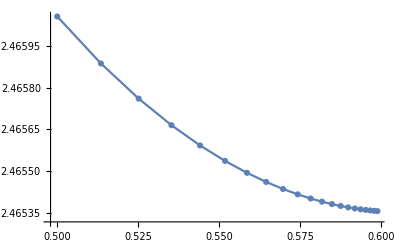

Time taken to find minimum: 62.6s

{ω_min,E_min}: {0.599673,2.46536}

Expectation Values pair {12, 23, 31}: {26.2977,35.1627,53.1947}

Expectation Values as ratios: {1.,1.3371,2.02279}

```mathematica
(* Find minimum *)
learningRate=1;
nSteps=30;
{minTime,min}=Timing[findMinimum[learningRate,nSteps]];
wMin=min[[1]];
data=min[[3]];

(* Plot gradient descent *)
Print["Plot of gradient descent."]
ListPlot[data,Joined->True,PlotMarkers->Automatic]

(* Print diagnostics *)
Print["Time taken to find minimum: ",DecimalForm[minTime,3],"s"]
Print["{ω_min,E_min}: ",{min[[1]],min[[2]]}]

(* Get expectation value of the delta function using the Subscript[ω, min] found *)
alphaIndex=1;(* Choose index of alpha Subscript[α, alphaIndex] *)
expValDelta[J,P,Isospin,Λ,γMax,wMin,m1,m2,m3,project,alphaIndex]
```

```mathematica
A3=((m1(m2+m3))/(m3(m1+m2)))^(1/2)
```

0.681264

```mathematica
(0.008704211/A3)
```

0.0127766

```mathematica
0.01277*5.068^3
```

1.66227

```mathematica
14.8/0.008217179107250
```

1801.1